```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

## Parameters

```mathematica
(*Approximations: complexes are in equilibrium, effectors are conserved.

 r+decoy <-->C
t+e --> (te)b-->e
c+e --> (ce)b-->a+e
		d+e --> (de)^b --> e
*)
```

```mathematica
gT=10; (*t growth*)
gR=1; (*NLR growth*)
gD=20; (*decoy growth*)
deltaT=1; (*t decay*)
deltaR=1; (*NLR decay*)
deltaD=1; (*decoy decay*)
beta1=1; (*effector-target affinity*)
beta2=1; (*effector-target unbinding*)
```

```mathematica
alphaF=0.5; (*R-T complex formation*)
alphaB=1; (*R-T complex unbinding*)
gamma1=1;  (*complex-effector binding*)
gamma2=5; (*complex-effector unbinding*)
```

```mathematica
e0=3; (*total effector concentration*)
```

```mathematica
(*test to see if low t recovers original dynamics*)
```

```mathematica
(*gT=0.000;
gD=10;*)
```

## Equations

```mathematica
(*solve for E based on e0 and quasi-equilibrium*)
```

```mathematica
fixedEEq=x+(beta1/beta2)*(tVar+dVar)*x+(gamma1/gamma2)*rVar*dVar*x*alphaF/(alphaB+gamma1*x)-e0Var==0;
fixedSol=x/.Solve[fixedEEq,x];
getE[thisR_?NumericQ,thisT_?NumericQ,thisD_?NumericQ,thisE0_?NumericQ]:=Module[{numericSol,final},

numericSol=fixedSol/.{rVar->thisR,tVar->thisT,dVar->thisD,e0Var->thisE0}//N;
Sort[numericSol];
If[(numericSol[[1]]<0)&&(numericSol[[2]]>0),final=numericSol[[2]],final="error"];
final
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
getZ[eVar_]:=Module[{thisZ},
(* return Z*)
thisZ=eVar*alphaF*gamma1/(alphaB+gamma1*eVar);
thisZ
]
```

```mathematica
drds[rVar_,tVar_,aVar_,dVar_,e0Var_]:=Module[{thisE,thisZ},

thisE=getE[rVar,tVar,dVar,e0Var];
thisZ=getZ[thisE];
gR-deltaR*rVar-rVar*dVar*thisZ+f[aVar]
]
```

```mathematica
dtds[rVar_,tVar_,dVar_,e0Var_]:=Module[{thisE,thisZ},
thisE=getE[rVar,tVar,dVar,e0Var];
thisZ=getZ[thisE];
gT-deltaT*tVar-beta1*tVar*thisE
]
```

```mathematica
dads[rVar_,tVar_,aVar_,dVar_,e0Var_]:=Module[{thisE,thisZ},

thisE=getE[rVar,tVar,dVar,e0Var];
thisZ=getZ[thisE];
rVar*dVar*thisZ-deltaR*aVar
]
(*dads=r[s]*t[s]*e*z;*)
```

```mathematica
ddds[rVar_,tVar_,dVar_,e0Var_]:=Module[{thisE,thisZ},

thisE=getE[rVar,tVar,dVar,e0Var];
thisZ=getZ[thisE];
gD-deltaD*dVar-rVar*dVar*thisZ-beta1*dVar*thisE
]
```

```mathematica
f[z_]:=z^2;(*feedback*)
```

## solver

```mathematica
(* remove duplicates *)
processRoots[rootList_]:=Module[{cleanList,test,unique,thisDist,i,j},
cleanList={rootList[[1]]};
For[i=2,i<=Length[rootList],i++,

test=rootList[[i]];
unique=True;
For[j=1,j<=Length[cleanList],j++,
	thisDist=EuclideanDistance[test,cleanList[[j]]];
	If[thisDist<10^-5,unique=False];
];
If[unique==True,AppendTo[cleanList,test];];

];

cleanList
]
```

```mathematica
getFixedPoint[e0Var_]:=Module[{rootList,thisSol,thisGuess,guessList,cleanList,i,j,k},

guessList={0.1,1,10,100};
rootList={};
Print[e0Var];
For[i=1,i<=Length[guessList],i++,
For[j=1,j<=Length[guessList],j++,
For[k=1,k<=Length[guessList],k++,

thisSol=FindRoot[{drds[rVar,tVar,aVar,dVar,e0Var]==0,dtds[rVar,tVar,dVar,e0Var]==0,dads[rVar,tVar,aVar,dVar,e0Var]==0,ddds[rVar,tVar,dVar,e0Var]==0},{rVar,guessList[[i]],0,10^6},{tVar,guessList[[j]],0,10^6},{aVar,guessList[[k]],0,10^6},{dVar,guessList[[j]],0,10^6}];
residual=(drds[rVar,tVar,aVar,dVar,e0Var])^2+(dtds[rVar,tVar,dVar,e0Var])^2+(dads[rVar,tVar,aVar,dVar,e0Var])^2+(ddds[rVar,tVar,dVar,e0Var])^2/.thisSol; (*check convergence*)
If[residual<=10^-6,AppendTo[rootList,{rVar,tVar,aVar,dVar}/.thisSol];];
];
];
];
cleanList=processRoots[rootList];
cleanList
]
```

```mathematica
e0List=Join[{0.001},Range[0.5,2.5,.5],Range[3,5,.1],Range[5.5,20,0.5]];
```

```mathematica
(*(e,list of fixed points)*)
fixedPointList=Table[{i,getFixedPoint[i]},{i,0,30,.1}];
```

0.

FindRoot::nlnum: The function value {0.91-(0.005 error)/(1.+error),9.9-0.1 error,-0.1+(0.005 error)/(1.+error),19.9-0.1 error-(0.005 error)/(1.+error)} is not a list of numbers with dimensions {4} at {rVar,tVar,aVar,dVar} = {0.1,0.1,0.1,0.1}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[{drds[rVar,tVar,aVar,dVar,0.]==0,dtds[rVar,tVar,dVar,0.]==0,dads[rVar,tVar,aVar,dVar,0.]==0,ddds[rVar,tVar,dVar,0.]==0},{rVar,guessList$21623⟦i$21623⟧,0,10^6},{tVar,guessList$21623⟦j$21623⟧,0,10^6},{aVar,guessList$21623⟦k$21623⟧,0,10^6},{dVar,guessList$21623⟦j$21623⟧,0,10^6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

0.1

FindRoot::reged: The point {0.,0.108815,9.99021,0.117856} is at the edge of the search region {0.,1.×10^6} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.,0.100019,99.9994,0.100394} is at the edge of the search region {0.,1.×10^6} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.,1.00623,9.99137,1.01459} is at the edge of the search region {0.,1.×10^6} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.2

0.3

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

0.4

0.5

0.6

0.7

0.8

0.9

1.

1.1

1.2

1.3

1.4

1.5

1.6

1.7

1.8

1.9

2.

2.1

2.2

2.3

2.4

2.5

2.6

2.7

2.8

2.9

3.

3.1

3.2

3.3

3.4

3.5

3.6

3.7

3.8

3.9

4.

4.1

4.2

4.3

4.4

4.5

4.6

4.7

4.8

4.9

5.

5.1

5.2

5.3

5.4

5.5

5.6

5.7

5.8

5.9

6.

6.1

6.2

6.3

6.4

6.5

6.6

6.7

6.8

6.9

7.

7.1

7.2

7.3

7.4

7.5

7.6

7.7

7.8

7.9

8.

8.1

8.2

8.3

8.4

8.5

8.6

8.7

8.8

8.9

9.

9.1

9.2

9.3

9.4

9.5

9.6

9.7

9.8

9.9

10.

10.1

10.2

10.3

10.4

10.5

10.6

10.7

10.8

10.9

11.

11.1

11.2

11.3

11.4

11.5

11.6

11.7

11.8

11.9

12.

12.1

12.2

12.3

12.4

12.5

12.6

12.7

12.8

12.9

13.

13.1

13.2

13.3

13.4

13.5

13.6

13.7

13.8

13.9

14.

14.1

14.2

14.3

14.4

14.5

14.6

14.7

14.8

14.9

15.

15.1

15.2

15.3

15.4

15.5

15.6

15.7

15.8

15.9

16.

16.1

16.2

16.3

16.4

16.5

16.6

16.7

16.8

16.9

17.

17.1

17.2

17.3

17.4

17.5

17.6

17.7

17.8

17.9

18.

18.1

18.2

18.3

18.4

18.5

18.6

18.7

18.8

18.9

19.

19.1

19.2

19.3

19.4

19.5

19.6

19.7

19.8

19.9

20.

20.1

20.2

20.3

20.4

20.5

20.6

20.7

20.8

20.9

21.

21.1

21.2

21.3

21.4

21.5

21.6

21.7

21.8

21.9

22.

22.1

22.2

22.3

22.4

22.5

22.6

22.7

22.8

22.9

23.

23.1

23.2

23.3

23.4

23.5

23.6

23.7

23.8

23.9

24.

24.1

24.2

24.3

24.4

24.5

24.6

24.7

24.8

24.9

25.

25.1

25.2

25.3

25.4

25.5

25.6

25.7

25.8

25.9

26.

26.1

26.2

26.3

26.4

26.5

26.6

26.7

26.8

26.9

27.

27.1

27.2

27.3

27.4

27.5

27.6

27.7

27.8

27.9

28.

28.1

28.2

28.3

28.4

28.5

28.6

28.7

28.8

28.9

29.

29.1

29.2

29.3

29.4

29.5

29.6

29.7

29.8

29.9

30.

```mathematica
(*convert a list where each e has a 3D ss, to coordinates for plotting. want r*(e), t*(e), a*(e)*)
getPlottingCoords[fixedPoints_]:=Module[{},

rPoints={};
tPoints={};
aPoints={};
dPoints={};

For[i=1,i<=Length[fixedPoints],i++,

thisPoint=fixedPoints[[i]];
eValue=thisPoint[[1]];

For[j=1,j<=Length[thisPoint[[2]]],j++,

thisFixedPoint=thisPoint[[2,j]];
AppendTo[rPoints,{eValue,thisFixedPoint[[1]]}];
AppendTo[tPoints,{eValue,thisFixedPoint[[2]]}];
AppendTo[aPoints,{eValue,thisFixedPoint[[3]]}];
AppendTo[dPoints,{eValue,thisFixedPoint[[4]]}];
];
];

{rPoints,tPoints,aPoints,dPoints}

]
```

```mathematica
{rCoords,tCoords,aCoords,dCoords}=getPlottingCoords[fixedPointList];
```

Part::partw: Part 3 of {}⟦1⟧ does not exist.

Part::partw: Part 4 of {}⟦1⟧ does not exist.

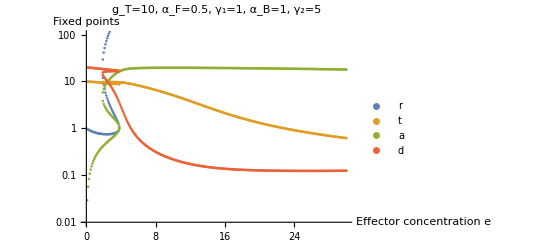

```mathematica
plot=ListLogPlot[{rCoords,tCoords,aCoords,dCoords},PlotRange->{Automatic,{.01,100}},PlotLabel->"g_T="<>ToString[gT]<>", α_F="<>ToString[alphaF]<>", γ_1="<>ToString[gamma1]<>", α_B="<>ToString[alphaB]<>", γ_2="<>ToString[gamma2],AxesLabel->{"Effector concentration e","Fixed points"},LabelStyle->Directive[Black, 10],PlotLegends->{"r","t","a","d"}]
```

```mathematica
Export["decoyPoints_gD_"<>ToString[gD]<>"_rtad.mx",{rCoords,tCoords,aCoords,dCoords}];
```

## fixed point complex formation

```mathematica
getComplex[rVar_,tVar_,e0Var_]:=rVar*tVar*alphaF/(alphaB+gamma1*getE[rVar,tVar,e0Var])
getBoundTarget[rVar_,tVar_,e0Var_]:=(beta1/beta2)*tVar*getE[rVar,tVar,e0Var];
getBoundComplex[rVar_,tVar_,e0Var_]:=(gamma1/gamma2)*getComplex[rVar,tVar,e0Var]*getE[rVar,tVar,e0Var];
```

```mathematica
(*given fixed points for r, t, a, compute E, complex, (te)^b,(Ce)^b, *)
(*output=(E0,((E1, complex1,boundTarget1,boundComplex1),(E2, complex2,boundTarget2,boundComplex2)...)*)
convertPoints[inputFixedPoints_]:=Module[{thisE0,pointList,thisBindingList,i,thisR,thisT,thisA,thisE,thisComplex,thisBoundComplex,thisBoundTarget,thisPoint,output},

thisE0=inputFixedPoints[[1]];
pointList=inputFixedPoints[[2]];
(*a list containing a list for each fixed point*)
thisBindingList={};
For[i=1,i<=Length[pointList],i++,

{thisR,thisT,thisA}=pointList[[i]];
thisE=getE[thisR,thisT,thisE0];
thisComplex=getComplex[thisR,thisT,thisE0];
thisBoundTarget=getBoundTarget[thisR,thisT,thisE0];
thisBoundComplex=getBoundComplex[thisR,thisT,thisE0];

thisPoint={thisE,thisComplex,thisBoundTarget,thisBoundComplex};

AppendTo[thisBindingList,thisPoint];
];

output={thisE0,thisBindingList}

]
```

```mathematica
(*convert a list where each e has a 3D ss, to coordinates for plotting. want r*(e), t*(e), a*(e)*)
getBoundPlottingCoords[boundPoints_]:=Module[{i,j,ePoints,complexPoints,boundTargetPoints,boundComplexPoints,thisPoint,eValue,thisFixedPoint},

ePoints={};
complexPoints={};
boundTargetPoints={};
boundComplexPoints={};

For[i=1,i<=Length[boundPoints],i++,

thisPoint=boundPoints[[i]];
eValue=thisPoint[[1]];

For[j=1,j<=Length[thisPoint[[2]]],j++,

thisFixedPoint=thisPoint[[2,j]];
AppendTo[ePoints,{eValue,thisFixedPoint[[1]]}];
AppendTo[complexPoints,{eValue,thisFixedPoint[[2]]}];
AppendTo[boundTargetPoints,{eValue,thisFixedPoint[[3]]}];
AppendTo[boundComplexPoints,{eValue,thisFixedPoint[[4]]}];
];
];

{ePoints,complexPoints,boundTargetPoints,boundComplexPoints}

]
```

```mathematica
(*calculate complexes from fixed points*)
```

```mathematica
allBoundFixedPoints=Table[convertPoints[fixedPointList[[i]]],{i,Length[fixedPointList]}];
```

Set::shape: Lists {thisR$6005783,thisT$6005783,thisA$6005783} and {}⟦1⟧ are not the same shape.

Set::shape: Lists {thisR$6005790,thisT$6005790,thisA$6005790} and {0.971476,9.96961,0.0293881,19.9099} are not the same shape.

Set::shape: Lists {thisR$6005793,thisT$6005793,thisA$6005793} and {0.946131,9.93907,0.0571332,19.8214} are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
(*convert to coordinates for plotting*)
{eCoords,complexCoords,boundTargetCoords,boundComplexCoords}=getBoundPlottingCoords[allBoundFixedPoints];
```

```mathematica
(*plot*)
```

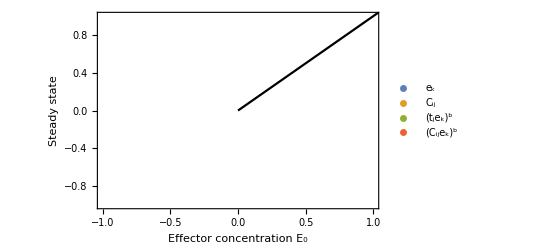

```mathematica
Show[ListPlot[{eCoords,complexCoords,boundTargetCoords,boundComplexCoords},PlotRange->{Automatic,Automatic},Frame->{True,True,False,False},FrameLabel->{"Effector concentration E_0","Steady state"},LabelStyle->Directive[Black, 12],PlotLegends->{"e_k","C_ij","(t_je_k)^b","(C_ije_k)^b"}],Plot[x,{x,0,6},PlotStyle->Black]]
```

```mathematica
(*Export["boundMolecules.png",%]*)
```

Part::partd: Part specification colors⟦2⟧ is longer than depth of object.

Part::partd: Part specification colors⟦4⟧ is longer than depth of object.

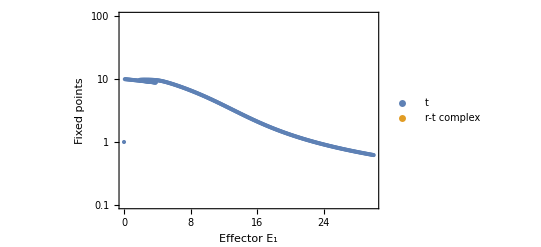

```mathematica
ListLogPlot[{tCoords,complexCoords},PlotRange->{Automatic,{.1,100}},Frame->{True,True,False,False},FrameLabel->{"Effector E_1","Fixed points"},LabelStyle->Directive[Black, 15],PlotLegends->{"t","r-t complex"},PlotStyle->{colors[[2]],colors[[4]]}]
```

```mathematica
(*Export["bifurcationPlot_tC.png",%,ImageResolution->400]*)
```